Science Fair Project

Barrant, Maurice

Keane, Kyle

Good Hope Country Day School

Most representative image

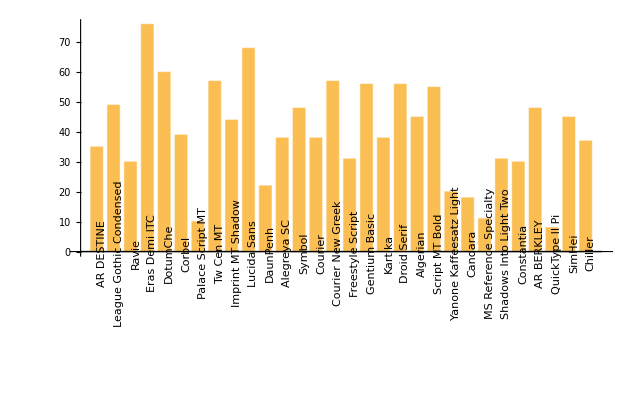

Abstract

GOAL OF THE PROJECT: Use Wolfram Language for Science Fair Projects

SUMMARY OF WORK: Demonstrate a possible science fair project that a high school student might be able to perform.

RESULTS AND FUTURE  WORK: Determine which science fair categories are best suited for the Wolfram Language.  Be able to make recommendations to students on direction their projects should go.  Be able to offer assistance using Wolfram Language.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail
Science Fair projects generally involve the following steps.
1. Topic selection - view the ISEF web page for the categories: https://student.societyforscience.org/intel-isef-categories-and-subcategories
2.  Problem statement
3.  Experiments
4.  Data collection
5.  Data analysis
6.  Results and conclusions

Code

```mathematica
numbers=RandomInteger[{0,9},100];
```

```mathematica
howGoodIsFont[numbers_][font_]:=Module[
{net,result},
net=NetModel[“LeNet Trained on MNIST Data”];
result=net[Rasterize[Style[#,FontFamily->font]]&/@numbers];
Count[SameQ@@@Thread[{result,numbers}],True]
]
```

```mathematica
results=AssociationMap[howGoodIsFont[numbers],RandomSample[$FontFamilies,30]];
```

```mathematica
BarChart[results,ChartLabels->Placed[Keys[results],Axis,Rotate[#,Pi/2] &]]
```

```mathematica
courierAlphabet=Rasterize[Style[#,FontFamily->”Courier New”]]& /@ Alphabet[]
```

```mathematica
alphaThread=Thread[courierAlphabet->Alphabet[]]
```

```mathematica
alphabetClassify =Classify[alphaThread]
```

```mathematica
comicFont=Rasterize[Style[#,FontFamily->”Comic Sans MS”]] & /@ Alphabet[]
```

```mathematica
alphabetClassify[comicFont]
```

Written Content / Lesson Plans

Conclusions in Detail

Supporting students in Science Fair projects can be fairly rewarding.  Finding topics that are meaningful for them is not a simple process but the Wolfram Language makes it possible for them to perform complex tasks without getting bogged down in the computation.  Students are challenged to learn the Wolfram Language and develop subject matter expertise.  Even though this topic seemed relatively simple, Neural Networks are limited in the datasets that have been built.  In this project, I was unable to compare the whole alphabet for each font because the dataset was limited to digits.  To expand this project students will need to learn how to create their own datasets and train the Neural Network.

All Visualizations

Data Sources Links/References

Future Directions

Social Media
Finance
Geography
Audio

Background Info Links/References

Keywords

Provide keywords as items

education

machine learning

high school

science fair

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```